```mathematica
CdW
```

# AeroAircraft6DOFSS

## Flight dynamics model of super-sonic aircraft

```mathematica
<<C:\\Hopsan\Compgen\CompgenNG.mx
```

```mathematica
Off[General::"spell1"]
```

```mathematica
path=ToFileName[{"C:","HopsanTrunk","ComponentLibraries","defaultLibrary","Special","AeroComponents"}];
```

Flight dynamics simulation is used in a wide range of applications from aircraft design to operations evaluation and flight training. This means that the models are to be used over very different time scales. For aircraft design very detailed flight dynamics characteristics needs to be evaluated, while much simplified models can be used for simualation of missions and to represent other planes in pilot training (and computer games). In order to meat these ends of the spectra the simulation models must incorporate a lot of detail while on the other hand be robust so that they can be used also with large time steps. Here the symbolic math packages Mathematica is used. By using symbolic manipulation high level differential algebraic equations can be transformed into low level code ( C++) where highly robust numerical solvers are integrated into the model, for highly efficient robust simulation.

-Graphics3D-

```mathematica
domain="Aero";
displayName="Aircraft6DOFSS";
brief="Flight dynamics model of super-sonic aircraft";
componentType="ComponentC";
author="Petter Krus <petter.krus@liu.se>";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFilenames[path,domain,displayName];
ResetComponentVariables[];
Date[]
```

{2015,9,18,12,43,22.415339}

## Defining node variables

```mathematica
Tafin=torfin; defin=thetafin;sdefin=wfin;cxfin=cfin;Zxfin=Zcfin;
Tal1=toral1; del1=thetaal1;sdel1=wal1;cxal1=cal1;Zxal1=Zcal1;
Tar1=torar1; der1=thetaar1;sder1=war1;cxar1=car1;Zxar1=Zcar1;
Tal12=toral12; del12=thetaal12;sdel12=wal12;cxal12=cal12;Zxal12=Zcal12;
Tar12=torar12; der12=thetaar12;sder12=war12;cxar12=car12;Zxar12=Zcar12;
Tal2=toral2; del2=thetaal2;sdel2=wal2;cxal2=cal2;Zxal2=Zcal2;
Tar2=torar2; der2=thetaar2;sder2=war2;cxar2=car2;Zxar2=Zcar2;
```

```mathematica
MechanicCnode[n_,position_,comment_]:={n,
{{f[n],0.,Real,"N","force"},
{x[n],position,Real,"m","position"},
{sx[n],0.,Real,"m/s","speed"},
{cx[n],0.,Real,"N","wave variable"},
{Zx[n],0.,Real,"N/m/s","Char. impedancs"}},"mechanicCnodes",comment}
```

## Loading Library

```mathematica
Derivative[1,0][Atan2][y_,x_]:=
D1Atan2[y,x];
```

```mathematica
Derivative[1,0][Atan2L][y_,x_]:=
D1Atan2L[y,x];
```

```mathematica
Derivative[0,1][Atan2][y_,x_]:=
D2Atan2[y,x];
```

```mathematica
Derivative[0,1][Atan2L][y_,x_]:=
D2Atan2L[y,x];
```

```mathematica
Derivative[1][ArcSinL][x_]:=
DArcSinL[x];
```

```mathematica
Derivative[1][SecL][x_]:=
DxSecL[x];

Unprotect[Sec];
Sec[x_]:=SecL[x]
```

## Component description

This model simulates a 3D model of an airplane.

### Parameters and variables used in this component.

#### Declarations

Alias for some variables

```mathematica
θ=Thetao;
ψ=Psi;
ϕ=Phi;
α=Alpha;
β=Beta;
Λ=Lambda1;
Γ=Gamma1;
```

```mathematica
Subscript[M, θ̇] =Mdvtheta;
Subscript[M, ψ̇]=Mdvpsi;
Subscript[M, OverDot[∅]]=.;
```

```mathematica
q = qpress;
q0=.;
q1=.;
q2=.;
q3=.;
```

#### Declarations of variables

The global output variables are those variables that are of interst outside the component.

```mathematica
outputVariables={
{xcg,0,double,"m","Horizontal position 1"},
{ycg,0,double,"m","Horizontal position 2"},
{zcg,0,double,"m","Vertical position"},
{vx,0,double,"m","Horizontal speed 1"},
{vy,0,double,"m","Horizontal speed 2"},
{vz,0,double,"m","Vertical speed"},
{ψ,0,double,"rad","Azimuth angle"},
{θ,0,double,"rad","Elevation angle"},
{ϕ,0,double,"rad","Bank angle"},
{Ub,100,double,"m/s","Speed xb-axis"},
{Vb,0,double,"m/s","Speed yb-axis"},
{Wb,0,double,"m/s","Speed zb-axis"},
{Pb,0,double,"rad/s","Angular velocity"},
{Qb,0,double,"rad/s","Angular velocity"},
{Rb,0,double,"rad/s","Angular velocity"},
{q0,0,double,"","quartenion 0"},
{q1,0,double,"","quartenion 1"},
{q2,0,double,"","quartenion 2"},
{q3,0,double,"","quartenion 3"},
{AlphaAttack,0,double,"rad","Angle of atack"},
{BetaSlip,0,double,"rad/s","Sideslip angle"},
{altitude,0,double,"m","altitude"},
{gfx,0,double,"m/s^2","g-force in x"},
{gfy,0,double,"m/s^2","g-force in y"},
{gfz,0,double,"m/s^2","g-force in z"},
{CL1,0,double,"","Lift coeff. wing 1"},
{Cd1,0,double,"","Drag coeff. wing 1"},
{Fax,0,double,"N","Aero force in z"},
{Faz,0,double,"N","Aero force in x"}
};
```

The input variables are those variables that are inputs during the simulation to the component. In practice thery are very similar to input parameters as the can be converted from each other in the Hopsan interface. It only effects the default settings in the component XML file.

```mathematica
inputVariables={
{thrustl,0.,double,"N","Engine thrust"},
{thrustr,0.,double,"N","Engine thrust"},
{dezthrustl,0.,double,"rad","Thrust angle"},
{dezthrustr,0.,double,"rad","Thrust angle"},
{deythrustl,0.,double,"rad","Thrust angle"},
{deythrustr,0.,double,"rad","Thrust angle"},
{Mfuel,0.,double,"kg","Fuel weight"},
{Mcargo,0.,double,"kg","Cargo weight"},
{rho,1.25,double,"kg/m3","Air density"},
{vM,340.,double,"m/s","Speed of sound"},
{vturbx,0.,double,"m/s","air turbulence x"},
{vturby,0.,double,"m/s","air turbulence y"},
{vturbz,0.,double,"m/s","air turbulence z"},
{wturbx,0.,double,"rad/s","air turbulence x"},
{wturby,0.,double,"rad/s","air turbulence y"},
{wturbz,0.,double,"rad/s","air turbulence z"}};
```

```mathematica
nodeConnections={
MechanicRotCnode[al1,0.,0.,"mechanical node left airleron 1"],
MechanicRotCnode[ar1,0.,0.,"mechanical node right airleron 1"],
MechanicRotCnode[al12,0.,0.,"mechanical node left flaperon 1"],
MechanicRotCnode[ar12,0.,0.,"mechanical node right flaperon 1"],
MechanicRotCnode[al2,0.,0.,"mechanical node left airleraon 2"],
MechanicRotCnode[ar2,0.,0.,"mechanical node right airleraon 2"],
MechanicRotCnode[fin,0.,0.,"mechanical node fin"]};
```

inptutParameters are parameters that are normally used throughout the whole system.

The local parameters are the component specific parameters. Default parameters are based on the F-16.
-Graphics-
Geometric data is entered in dimensionless form that relates to the actual data through the reference area and the aspect ratio.

```mathematica
inputParameters={
{afin,0.3,double,"rad","break angle 1"},
{an1,0.6,double,"rad","Neg. break angle 1"},
{an2,0.6,double,"rad","Neg. break angle 2"},
{ap1,0.9,double,"rad","Pos. break angle 1"},
{ap2,0.7,double,"rad","Pos. break angle 2"},
{AR1,3.62,double,"","Aspect ratio 1"},
{AR2,3.62,double,"","Aspect ratio 2"},
{ARfin,1.5,double,"","Aspect ratio fin"},
{Cd01,0.0045,double,"","Drag coef. 1"},
{Cd02,0.0045,double,"","Drag coef. 2"},
{Cd0b,0.03,double,"","Drag coef. body"},
{Cd0fin,0.0045,double,"","Drag coef. fin"},
{CdW0,0.048,double,"","Wave drag coef."},
{CLalpha1,2.1,double,"","L. slope coef. 1"},
{CLalpha2,2.2,double,"","L. slope coef. 2"},
{CLalphabh,2.,double,"","L. slope c. body h"},
{CLalphabv,2.,double,"","L. slope c. bodyv"},
{CLalphafin,0.80,double,"","L. sl. c. fin"},
{CLde1,0.1,double,"","Ctrl surface coef 1"},
{CLde12,0.2,double,"","Flap rudder coef 1"},
{Cdide1,0.,double,"","Flap rudder drag coef 1"},
{Cdide12,0.,double,"","Flap rudder drag coef 1"},
{Cdide112,0.,double,"","Flap rudder cross drag coef 1"},
{de10,0.01,double,"","rudder min drag angle 1"},
{de120,0.01,double,"","Flap min drag angle 1"},
{dM,0.1,double,"","Width of transonic region (rel. Mach)"},
{Cm01,-0.1,double,"","Mom coeff. wing 1"},
{Cmfs1,-0.5,double,"","Mom coeff.1, fully separated"},
{Cmde1,0.02,double,"","Mom slop coeff 1"},
{Cmde12,0.1,double,"","Flap Mom slop coeff 1"},
{CLdefin,0.0827084,double,"","Rudder coef 1"},
{Cydeelev,0.1,double,"","elevator side force coef"},
{dah1,1.0,double,"","down wash effect on 1"},
{dah2,0.6,double,"","down wash effect on 2"},
{en,2.71828,double,"","e"},
{e1,0.95,double,"","Osw. effic. factor 1"},
{e2,0.95,double,"","Osw. effic. factor 21"},
{efin,0.95,double,"","Osw. eff. f. fin"},
{epsM,0.3,double,"","Mach smoothening factor"},
{awfin,.2,double,"","CL exponent fin"},
{awn1,.2,double,"","CL exponent neg. 1"},
{awn2,.2,double,"","CL exponent neg. 2"},
{awp1,.2,double,"","CL exponent pos 1"},
{awp2,.2,double,"","CL exponent neg 1"},
{gamma1,-0.0872665,double,"rad","dehidral"},
{gamma2,-0.0872665,double,"rad","dehidral"},
{hthrust0,0.,double,"","engine vert. pos"},
{ia1,0.,double,"rad","incidence angle 1"},
{ia2,0.02,double,rad"","incidence angle 1"},
{Ix0,0.0147,double," ","Norm. Inertia moment Ix/(Me S1)"},
{Ixz0,0.0055,double," ","Norm. Inertia moment"},
{Iy0,1.131,double," ","Norm. Inertia moment"},
{Iz0,1.279,double," ","Inertia moment"},
{lambda1,0.436332,double,"rad","sweep 1"},
{lambda2,0.436332,double,"rad","sweep 2"},
{lambdafin,0.785398,double,"rad","sweep fin"},
{lc10,0.01,double,"","norm. ctrl surf. 1 ac fr hinge lc1/sqrt(AR1 S1)"},
{lc20,0.05,double,"","norm. ctrl surf. 2 ac fr hinge lc1/sqrt(AR1 S1)"},
{lc120,0.01,double,"","norm. flap 1 ac fr hinge"},
{lcfin0,0.01,double,"","ctrl s. fin ac fr hinge"},
{Me,8700.,double,"kg","Empty weight"},
{mac0,1.,double,"","mean aerodynamic cord/Sqrt(S1/b1)"},
{rc10,0.25,double,"","norm. ctrl surface 1 mom. arm"},
{rc120,0.25,double,"","norm. ctrl surface 12 mom. arm"},
{rc20,0.15,double,"","norm. ctrl surface 1 mom. arm"},
{rcfin0,.1,double,"","norm. ctrl surf. fin mom. arm"},
{S1,27.,double,"m2","wing area 1"},
{S20,0.36,double,"","norm. wing area 2"},
{Sbh0,0.2,double,"","norm. hor. proj. area"},
{Sbv0,0.1,double,"","norm.body vert. proj. area"},
{Sfin0,0.17,double,"","norm. fin area"},
{xbach0,3,double,"","norm. body ac. hor."},
{xbacv0,3,double," ","norm. body ac vert."},
{xbcge0,3,double," ","norm. body cg"},
{xcargo0,3,double," ","norm. cargo pos."},
{xfuel0,3,double," ",""},
{xw10,3,double," ","norm. wing1  position"},
{xw20,4.8,double," ","norm. wing 2 position"},
{xwfin0,4.8,double,"","norm. fin position"},
{xeng0,4.8,double,"","norm. fin position"},
{yeng0,0.,double,"","engines off. from center"},
{g0,9.81,double,"m/s^2","Gravity acceleration"},
{kground,10000.,double,"N/m","Ground stiffness (for limitiation)"},
{cground,1000.,double,"Ns/m","Ground damping (for limitiation)"}};
```

The Qnodes are the connections to other components

```mathematica
Qnodes = {};
```

There are also a constants. Noiter is the number of iterations performed in each time step

### Nomenclature

L_BV         :Transformation matrix, body coordinates to vehicle-carried vertical frame

## Component equations

### Definitions

```mathematica
ζ:=({{1, Sin[ϕ]Tan[θ], Cos[ϕ]Tan[θ]}, {0, Cos[ϕ], -Sin[ϕ]}, {0, Sin[ϕ]SecL[θ], Cos[ϕ]SecL[θ]}})
```

The transformation matrices for transformation from body to earth axis are (Etkin (4.5,2)

```mathematica
Subscript[L, x][ϕ_]:=({{1, 0, 0}, {0, Cos[ϕ], Sin[ϕ]}, {0, -Sin[ϕ], Cos[ϕ]}})
```

```mathematica
Subscript[L, y][θ_] :=({{Cos[θ], 0, -Sin[θ]}, {0, 1, 0}, {Sin[θ], 0, Cos[θ]}})
```

```mathematica
Subscript[L, z][ψ_]:=({{Cos[ψ], Sin[ψ], 0}, {-Sin[ψ], Cos[ψ], 0}, {0, 0, 1}})
```

Transformation from vehicle-carried vertical frame to body coordinates can be expressed as (Etkin 4.5,3)

```mathematica
Subscript[L, BV]:=Subscript[L, x][ϕ].Subscript[L, y][θ].Subscript[L, z][ψ]
```

```mathematica
MatrixForm[Subscript[L, BV] ]
```

(Cos[Psi] Cos[Thetao] | Cos[Thetao] Sin[Psi] | -Sin[Thetao]
-Cos[Phi] Sin[Psi]+Cos[Psi] Sin[Phi] Sin[Thetao] | Cos[Phi] Cos[Psi]+Sin[Phi] Sin[Psi] Sin[Thetao] | Cos[Thetao] Sin[Phi]
Sin[Phi] Sin[Psi]+Cos[Phi] Cos[Psi] Sin[Thetao] | -Cos[Psi] Sin[Phi]+Cos[Phi] Sin[Psi] Sin[Thetao] | Cos[Phi] Cos[Thetao])

(Cos[Psi] Cos[Thetao] | Cos[Thetao] Sin[Psi] | -Sin[Thetao]
-Cos[Phi] Sin[Psi]+Cos[Psi] Sin[Phi] Sin[Thetao] | Cos[Phi] Cos[Psi]+Sin[Phi] Sin[Psi] Sin[Thetao] | Cos[Thetao] Sin[Phi]
Sin[Phi] Sin[Psi]+Cos[Phi] Cos[Psi] Sin[Thetao] | -Cos[Psi] Sin[Phi]+Cos[Phi] Sin[Psi] Sin[Thetao] | Cos[Phi] Cos[Thetao])

This can also be expressed using quartenions

```mathematica
Subscript[L, BV]:=({{q0^2+q1^2-q2^2-q3^2, 2 (q1 q2+q0 q3), 2 (-q0 q2+q1 q3)}, {2 (q1 q2-q0 q3), q0^2-q1^2+q2^2-q3^2, 2 (q0 q1+q2 q3)}, {2 (q0 q2+q1 q3), 2 (-q0 q1+q2 q3), q0^2-q1^2-q2^2+q3^2}})
```

where the quartenions can be expressed as below. The inital values of the quartenions are caluclated using these expressions

```mathematica
initialExpressions={
{q0,Cos[ϕ/2]Cos[θ/2]Cos[ψ/2]+Sin[ϕ/2]Sin[θ/2]Sin[ψ/2]},
{q1,Sin[ϕ/2]Cos[θ/2]Cos[ψ/2]-Cos[ϕ/2]Sin[θ/2]Sin[ψ/2]},
{q2,Cos[ϕ/2]Sin[θ/2]Cos[ψ/2]+Sin[ϕ/2]Cos[θ/2]Sin[ψ/2]},
{q3,Cos[ϕ/2]Cos[θ/2]Sin[ψ/2]-Sin[ϕ/2]Sin[θ/2]Cos[ψ/2]}}
```

{{q0,Cos[Phi/2] Cos[Psi/2] Cos[Thetao/2]+Sin[Phi/2] Sin[Psi/2] Sin[Thetao/2]},{q1,Cos[Psi/2] Cos[Thetao/2] Sin[Phi/2]-Cos[Phi/2] Sin[Psi/2] Sin[Thetao/2]},{q2,Cos[Thetao/2] Sin[Phi/2] Sin[Psi/2]+Cos[Phi/2] Cos[Psi/2] Sin[Thetao/2]},{q3,Cos[Phi/2] Cos[Thetao/2] Sin[Psi/2]-Cos[Psi/2] Sin[Phi/2] Sin[Thetao/2]}}

Conversly the total transformation matrix from body coordinates to vehicle-carried vertical frame is thus:

```mathematica
Subscript[L, VB] :=Transpose[Subscript[L, BV]]
```

```mathematica
MatrixForm[Subscript[L, VB] ]
```

(q0^2+q1^2-q2^2-q3^2 | 2 (q1 q2-q0 q3) | 2 (q0 q2+q1 q3)
2 (q1 q2+q0 q3) | q0^2-q1^2+q2^2-q3^2 | 2 (-q0 q1+q2 q3)
2 (-q0 q2+q1 q3) | 2 (q0 q1+q2 q3) | q0^2-q1^2-q2^2+q3^2)

When Euler angles are used, the state vector stateVariables of the system is defined as:

stateVariables={Ub,Vb,Wb,Pb,Qb,Rb,ϕ,θ,ψ,xcg,ycg,zcg};

When quartenions are used it instead becomes:

```mathematica
systemVariables = {Ub,Vb,Wb,Pb,Qb,Rb,q0,q1,q2,q3,xcg,ycg,zcg};
```

```mathematica
variableLowLimits={xcg,0.}
```

{xcg,0.}

Ω_B is from Stevensson and Lewis (1.5-2),

```mathematica
Subscript[Ω, B]:=({{0, -Rb, Qb}, {Rb, 0, -Pb}, {-Qb, Pb, 0}})
```

```mathematica
Subscript[Ω, q]:=({{0, Pb, Qb, Rb}, {-Pb, 0, -Rb, Qb}, {-Qb, Rb, 0, -Pb}, {-Rb, -Qb, Pb, 0}})
```

```mathematica
J:=({{Ix, 0, -Ixz}, {0, Iy, 0}, {-Ixz, 0, Iz}})
```

The invers of the inertia matrix is

```mathematica
Jinv:=Simplify [Inverse[J]]
```

The speed vector in body coordinates

```mathematica
Subscript[V, body]:={Ub,Vb,Wb}
```

The speed vector in earth coordinates

```mathematica
Subscript[V, NED]:={s xcg, s ycg, s zcg}
```

The force vector in body coordinates

```mathematica
Subscript[F, b] := {Fx,Fy,Fz}
```

The gravitational vector is defined as (earth coordinates):

```mathematica
Subscript[G, 0]:={0,0,g0}
Fground:={0,0,-onPositive[zcg]kground zcg}
```

The vector of Euler angles is:

Φ :={ϕ, θ,ψ}

The quartenion vector is:

```mathematica
quart:={q0,q1,q2,q3}
```

The angular rates in body coordinates

```mathematica
Subscript[ω, b]:={Pb,Qb,Rb}
```

The vector of moments in body coordinates

```mathematica
Subscript[T, b]:={Lb,Mb,Nb}
```

### The system equations

Force Equations

```mathematica
forceEquation:=s Subscript[V, body]-(-Subscript[Ω, B].Subscript[V, body]+Subscript[L, BV] .  (Subscript[G, 0]+Fground/mass)+Subscript[F, b]/mass)
```

Kinematic Equations

(when Euler angles are used)

kinematicEquation:=s Φ-ζ. ω_b

(when quartenions are used)

```mathematica
kinematicEquation:=s quart -(-1/2 Subscript[Ω, q].quart)
```

Moment Equations

```mathematica
momentEquation:=Simplify[s Subscript[ω, b]-(-Jinv .Subscript[Ω, B] .J . Subscript[ω, b]+Jinv. Subscript[T, b])]
```

Naviagation Equations

```mathematica
navigationEquation:=Subscript[V, NED]-Subscript[L, VB].Subscript[V, body]
```

Tranformation between quartenions and Euler angles can be done in a straightforward way by simply adding this set of equation to the systemEquationDa.

```mathematica
quartenion2Euler:={
q1-(Sin[ϕ/2]Cos[θ/2]Cos[ψ/2]-Cos[ϕ/2]Sin[θ/2]Sin[ψ/2]),
q2-(Cos[ϕ/2]Sin[θ/2]Cos[ψ/2]+Sin[ϕ/2]Cos[θ/2]Sin[ψ/2]),
q3-(Cos[ϕ/2]Cos[θ/2]Sin[ψ/2]-Sin[ϕ/2]Sin[θ/2]Cos[ψ/2])
}
```

A (marginally) more computationally efficient way, however, is to calculate them explicitly (which is used here).

```mathematica
Subscript[ϕ, expr]=Atan2L[2(q2 q3+q0 q1),q0^2-q1^2-q2^2+q3^2];
Subscript[θ, expr]=ArcSinL[2(q0 q2-q1 q3)];
Subscript[ψ, expr]=Atan2L[2(q1 q2+q0 q3),q0^2+q1^2-q2^2-q3^2];
```

To solve the system of equations all equations are equal to zero.

Another instance of the navigation equation is needed to obtain the speeds i earth coordinates.

```mathematica
expressionVE:=Transpose[{{vx,vy,vz},Subscript[L, VB].Subscript[V, body]}]
```

### Assembling the system of equations

```mathematica
forceEquation//TableForm
```

-Fx/mass+s Ub-Rb Vb+Qb Wb-2 (-q0 q2+q1 q3) (g0-(kground zcg onPositive[zcg])/mass)
-Fy/mass+Rb Ub+s Vb-Pb Wb-2 (q0 q1+q2 q3) (g0-(kground zcg onPositive[zcg])/mass)
-Fz/mass-Qb Ub+Pb Vb+s Wb-(q0^2-q1^2-q2^2+q3^2) (g0-(kground zcg onPositive[zcg])/mass)

```mathematica
momentEquation//TableForm
```

(-Iz^2 Qb Rb+Iz (Lb+Ixz Pb Qb+Iy Qb Rb-Ix Pb s)+Ixz (Nb+Ix Pb Qb-Iy Pb Qb-Ixz Qb Rb+Ixz Pb s))/(Ixz^2-Ix Iz)
(-Mb+Ix Pb Rb-Iz Pb Rb+Ixz (Pb^2-Rb^2)+Iy Qb s)/Iy
(Ixz (Lb-(Ix-Iy+Iz) Qb Rb)+Ixz^2 (Pb Qb+Rb s)+Ix (Nb+Ix Pb Qb-Iy Pb Qb-Iz Rb s))/(Ixz^2-Ix Iz)

```mathematica
kinematicEquation//TableForm
```

1/2 (Pb q1+q2 Qb+q3 Rb)+q0 s
1/2 (-Pb q0+q3 Qb-q2 Rb)+q1 s
1/2 (-Pb q3-q0 Qb+q1 Rb)+q2 s
1/2 (Pb q2-q1 Qb-q0 Rb)+q3 s

```mathematica
navigationEquation//TableForm
```

-(q0^2+q1^2-q2^2-q3^2) Ub-2 (q1 q2-q0 q3) Vb-2 (q0 q2+q1 q3) Wb+s xcg
-2 (q1 q2+q0 q3) Ub-(q0^2-q1^2+q2^2-q3^2) Vb-2 (-q0 q1+q2 q3) Wb+s ycg
-2 (-q0 q2+q1 q3) Ub-2 (q0 q1+q2 q3) Vb-(q0^2-q1^2-q2^2+q3^2) Wb+s zcg

#### The assembled set of equations

```mathematica
systemEquationsDa:=Flatten[{forceEquation,momentEquation,kinematicEquation,navigationEquation}]
```

```mathematica
boundaryEquations={};
```

```mathematica
systemEquationsDa//TableForm
```

-Fx/mass+s Ub-Rb Vb+Qb Wb-2 (-q0 q2+q1 q3) (g0-(kground zcg onPositive[zcg])/mass)
-Fy/mass+Rb Ub+s Vb-Pb Wb-2 (q0 q1+q2 q3) (g0-(kground zcg onPositive[zcg])/mass)
-Fz/mass-Qb Ub+Pb Vb+s Wb-(q0^2-q1^2-q2^2+q3^2) (g0-(kground zcg onPositive[zcg])/mass)
(-Iz^2 Qb Rb+Iz (Lb+Ixz Pb Qb+Iy Qb Rb-Ix Pb s)+Ixz (Nb+Ix Pb Qb-Iy Pb Qb-Ixz Qb Rb+Ixz Pb s))/(Ixz^2-Ix Iz)
(-Mb+Ix Pb Rb-Iz Pb Rb+Ixz (Pb^2-Rb^2)+Iy Qb s)/Iy
(Ixz (Lb-(Ix-Iy+Iz) Qb Rb)+Ixz^2 (Pb Qb+Rb s)+Ix (Nb+Ix Pb Qb-Iy Pb Qb-Iz Rb s))/(Ixz^2-Ix Iz)
1/2 (Pb q1+q2 Qb+q3 Rb)+q0 s
1/2 (-Pb q0+q3 Qb-q2 Rb)+q1 s
1/2 (-Pb q3-q0 Qb+q1 Rb)+q2 s
1/2 (Pb q2-q1 Qb-q0 Rb)+q3 s
-(q0^2+q1^2-q2^2-q3^2) Ub-2 (q1 q2-q0 q3) Vb-2 (q0 q2+q1 q3) Wb+s xcg
-2 (q1 q2+q0 q3) Ub-(q0^2-q1^2+q2^2-q3^2) Vb-2 (-q0 q1+q2 q3) Wb+s ycg
-2 (-q0 q2+q1 q3) Ub-2 (q0 q1+q2 q3) Vb-(q0^2-q1^2-q2^2+q3^2) Wb+s zcg

### The Forces and Moments Acting on the Aircraft

-Graphics--Graphics-
The forces and moments acting on the aircraft are aerodynamic forces and moments and forces and moments from the engine

```mathematica
aircraft`F := aircraft`aero`F + engine`F + ground`F;
aircraft`T := aircraft`aero`T + engine`T;
```

torque on x-axis

Lb := aircraft`T[[1]][[1]]

The aerodynamic forces acting on the airplane (expressed in wind coordinates) can be expressed as:

```mathematica
aircraft`aero`Fw:=wing1`aero`F+wing2`aero`F+fin`aero`F+body`aero`F
```

Transformed into body coordinates

```mathematica
aircraft`aero`F:=Subscript[L, BW].aircraft`aero`Fw
```

where the transformation matrix from wind to body coordinates is:

```mathematica
Subscript[L, BW] = Subscript[L, y][α].Subscript[L, z][-β];
```

```mathematica
aircraft`aero`Tw:=wing1`aero`T+wing2`aero`T+fin`aero`T+body`aero`T
```

Moments in body coordinates

```mathematica
aircraft`aero`T:=Subscript[L, BW].aircraft`aero`Tw
```

```mathematica
aircraft`aero`T:=aircraft`aero`Tw
```

#### Wing

The contributions from the wing are

```mathematica
wing1`aero`F:=({{-Dragl1-Dragr1}, {0}, {-Liftl1-Liftr1}})
```

```mathematica
wing1`aero`T:=({{-Subscript[M, OverDot[∅]] Pbe+(Liftl1-Liftr1)rc1}, {(xbcg-xw1) ((Liftl1+Liftr1) Cos[α]+(Dragl1+Dragr1) Sin[α])+Moment1}, {(-Dragl1+Dragr1)rc1}})
```

Calculating the rudder hinge forces and aerodynamic stiffness

```mathematica
kal1:=CLde1 S1 q lc1;
kar1:=CLde1 S1 q lc1;
kal12:=CLde12 S1 q lc12;
kar12:=CLde12 S1 q lc12;
```

Rudder forces (wave variables for connection nodes)

```mathematica
exprW1={
{cxal1,kal1 (del1+α)} ,
{cxar1,kar1(der1+α)} ,
{cxal12,kal12 (del12+α)} ,
{cxar12,kar12(der12+α)}};
```

#### Horizontal tail

The contributions from the horizontal tail are

Forces

```mathematica
wing2`aero`F:=({{-Dragl2-Dragr2}, {-Cy2}, {-Liftl2-Liftr2}})
```

Moments

```mathematica
wing2`aero`T:=({{(Liftl2-Liftr2)rc2}, {-Subscript[M, θ̇] Qbe+((Liftl2+Liftr2) Cos[α]-(Dragl2+Dragr2) Sin[α]-Cl2-Cr2) (xbcg-xw2)}, {(-Dragl2+Dragr2)rc2}})
```

Rudder hinge forces and aerodynamic stiffness

```mathematica
kal2:=CLalpha2e S2 q lc2;
kar2:=CLalpha2e S2 q lc2;
```

```mathematica
exprW2={
{cxal2,kal2 (del2+α)} ,
{cxar2,kar2(der2+α)} };
```

#### Fin

-Graphics-
The contributions from the vertical tail are

Forces

```mathematica
fin`aero`F:=({{-Dragfin}, {-Cfin}, {0}})
```

Moments

```mathematica
fin`aero`T:=({{0}, {0}, {-Cfin (xwfin-xbcg)-Rbe Subscript[M, ψ̇]}})
```

Rudder hinge forces and aerodynamic stiffness

```mathematica
kafin:=CLdefin Sfin q lcfin;
```

```mathematica
exprFin={
{cxfin,kafin (defin+β)}
};
```

#### Body

The contributions from the body are

Forces

```mathematica
body`aero`F:=({{-Dragb}, {-Cbody}, {-Liftb}})
```

Moments

```mathematica
body`aero`T:=({{0}, {0}, {0}})
```

#### Propulsion

The thrust vector in body coordinates is

```mathematica
engine`T:={
yeng(thrustl Sin[dezthrustl] Cos[deythrustl]-thrustr Sin[dezthrustr] Cos[deythrustr]),
-(xeng-xbcg)(thrustl Sin[dezthrustl]Cos[deythrustl]+thrustr Sin[dezthrustr]Cos[deythrustr]) ,
-(xeng-xbcg)(thrustl Cos[dezthrustl] Sin[deythrustl] +thrustr Cos[dezthrustr] Sin[deythrustr])  
};
```

```mathematica
engine`F := {thrustl Cos[deythrustl]Cos[dezthrustr]+thrustr Cos[deythrustr]Cos[dezthrustr],
-thrustl Sin[deythrustl]Cos[dezthrustr]-thrustr Sin[deythrustr]Cos[dezthrustr],
-thrustl Cos[deythrustl]Sin[dezthrustr]-thrustr Cos[deythrustr]Sin[dezthrustr]
}
```

The total force an moment vectors in body coordinates are then

```mathematica
ground`F:=({{0}, {0}, {0}})
```

With ground limitation

```mathematica
ground`F:=({{0}, {0}, {-onPositive[zcg]kground zcg}})
```

### Display forces and moments

The inverse of the inertia matrix

```mathematica
Jinv//MatrixForm
```

(Iz/(-Ixz^2+Ix Iz) | 0 | Ixz/(-Ixz^2+Ix Iz)
0 | 1/Iy | 0
Ixz/(-Ixz^2+Ix Iz) | 0 | Ix/(-Ixz^2+Ix Iz))

```mathematica
wing1`aero`F//MatrixForm
```

(-Dragl1-Dragr1
0
-Liftl1-Liftr1)

```mathematica
wing1`aero`T//MatrixForm
```

((Liftl1-Liftr1) rc1-(Pb+(q0^2+q1^2-q2^2-q3^2) wturbx+2 (q1 q2-q0 q3) wturby+2 (q0 q2+q1 q3) wturbz) M_OverDot[∅]
qpress S1 (-Cmde1 thetaal1-Cmde12 thetaal12-Cmde1 thetaar1-Cmde12 thetaar12-(smc (CLde1 thetaal1+CLde12 thetaal12+1/2 CLift[Alpha dah1-ia1,CLalpha1e,ap1,an1,awp1,awn1]))/(4 (1+en^(-(2 (v-(1-dM) vM))/(dM vM))))-(smc (CLde1 thetaar1+CLde12 thetaar12+1/2 CLift[Alpha dah1-ia1,CLalpha1e,ap1,an1,awp1,awn1]))/(4 (1+en^(-(2 (v-(1-dM) vM))/(dM vM))))+CMoment[Alpha dah1-ia1,Cm01,Cmfs1,ap1,an1,awp1,awn1])+(xbcg-xw1) ((Liftl1+Liftr1) Cos[Alpha]+(Dragl1+Dragr1) Sin[Alpha])
(-Dragl1+Dragr1) rc1)

```mathematica
wing2`aero`F//MatrixForm
```

(-Dragl2-Dragr2
-Cydeelev qpress S2 (thetaal2-thetaar2)
-Liftl2-Liftr2)

```mathematica
wing2`aero`T//MatrixForm
```

((Liftl2-Liftr2) rc2
-Mdvtheta (Qb+2 (q1 q2+q0 q3) wturbx+(q0^2-q1^2+q2^2-q3^2) wturby+2 (-q0 q1+q2 q3) wturbz)+(xbcg-xw2) (-Cl2-Cr2+(Liftl2+Liftr2) Cos[Alpha]-(Dragl2+Dragr2) Sin[Alpha])
(-Dragl2+Dragr2) rc2)

```mathematica
fin`aero`F//MatrixForm
```

(-Dragfin
-Cfin
0)

```mathematica
fin`aero`T//MatrixForm
```

(0
0
-Mdvpsi (Rb+2 (-q0 q2+q1 q3) wturbx+2 (q0 q1+q2 q3) wturby+(q0^2-q1^2-q2^2+q3^2) wturbz)-Cfin (-xbcg+xwfin))

```mathematica
body`aero`F//MatrixForm
```

(-Dragb
CLalphabv qpress Sbv Sin[Beta]
-Liftb)

```mathematica
body`aero`T//MatrixForm
```

(0
0
0)

```mathematica
engine`F//MatrixForm
```

(thrustl Cos[deythrustl] Cos[dezthrustr]+thrustr Cos[deythrustr] Cos[dezthrustr]
-thrustl Cos[dezthrustr] Sin[deythrustl]-thrustr Cos[dezthrustr] Sin[deythrustr]
-thrustl Cos[deythrustl] Sin[dezthrustr]-thrustr Cos[deythrustr] Sin[dezthrustr])

```mathematica
engine`T//MatrixForm
```

(yeng (thrustl Cos[deythrustl] Sin[dezthrustl]-thrustr Cos[deythrustr] Sin[dezthrustr])
(xbcg-xeng) (thrustl Cos[deythrustl] Sin[dezthrustl]+thrustr Cos[deythrustr] Sin[dezthrustr])
(xbcg-xeng) (thrustl Cos[dezthrustl] Sin[deythrustl]+thrustr Cos[dezthrustr] Sin[deythrustr]))

```mathematica
aircraft`F//MatrixForm
```

((-Dragb-Dragfin-Dragl1-Dragl2-Dragr1-Dragr2) Cos[Alpha] Cos[Beta]+thrustl Cos[deythrustl] Cos[dezthrustr]+thrustr Cos[deythrustr] Cos[dezthrustr]-(-Liftb-Liftl1-Liftl2-Liftr1-Liftr2) Sin[Alpha]-Cos[Alpha] Sin[Beta] (-Cfin-Cydeelev qpress S2 (thetaal2-thetaar2)+CLalphabv qpress Sbv Sin[Beta])
(-Dragb-Dragfin-Dragl1-Dragl2-Dragr1-Dragr2) Sin[Beta]+Cos[Beta] (-Cfin-Cydeelev qpress S2 (thetaal2-thetaar2)+CLalphabv qpress Sbv Sin[Beta])-thrustl Cos[dezthrustr] Sin[deythrustl]-thrustr Cos[dezthrustr] Sin[deythrustr]
(-Liftb-Liftl1-Liftl2-Liftr1-Liftr2) Cos[Alpha]-kground zcg onPositive[zcg]+(-Dragb-Dragfin-Dragl1-Dragl2-Dragr1-Dragr2) Cos[Beta] Sin[Alpha]-Sin[Alpha] Sin[Beta] (-Cfin-Cydeelev qpress S2 (thetaal2-thetaar2)+CLalphabv qpress Sbv Sin[Beta])-thrustl Cos[deythrustl] Sin[dezthrustr]-thrustr Cos[deythrustr] Sin[dezthrustr])

```mathematica
aircraft`T//MatrixForm
```

((Liftl1-Liftr1) rc1+(Liftl2-Liftr2) rc2+yeng (thrustl Cos[deythrustl] Sin[dezthrustl]-thrustr Cos[deythrustr] Sin[dezthrustr])-(Pb+(q0^2+q1^2-q2^2-q3^2) wturbx+2 (q1 q2-q0 q3) wturby+2 (q0 q2+q1 q3) wturbz) M_OverDot[∅]
-Mdvtheta (Qb+2 (q1 q2+q0 q3) wturbx+(q0^2-q1^2+q2^2-q3^2) wturby+2 (-q0 q1+q2 q3) wturbz)+qpress S1 (-Cmde1 thetaal1-Cmde12 thetaal12-Cmde1 thetaar1-Cmde12 thetaar12-(smc (CLde1 thetaal1+CLde12 thetaal12+1/2 CLift[Alpha dah1-ia1,CLalpha1e,ap1,an1,awp1,awn1]))/(4 (1+en^(-(2 (v-(1-dM) vM))/(dM vM))))-(smc (CLde1 thetaar1+CLde12 thetaar12+1/2 CLift[Alpha dah1-ia1,CLalpha1e,ap1,an1,awp1,awn1]))/(4 (1+en^(-(2 (v-(1-dM) vM))/(dM vM))))+CMoment[Alpha dah1-ia1,Cm01,Cmfs1,ap1,an1,awp1,awn1])+(xbcg-xw1) ((Liftl1+Liftr1) Cos[Alpha]+(Dragl1+Dragr1) Sin[Alpha])+(xbcg-xw2) (-Cl2-Cr2+(Liftl2+Liftr2) Cos[Alpha]-(Dragl2+Dragr2) Sin[Alpha])+(xbcg-xeng) (thrustl Cos[deythrustl] Sin[dezthrustl]+thrustr Cos[deythrustr] Sin[dezthrustr])
(-Dragl1+Dragr1) rc1+(-Dragl2+Dragr2) rc2-Mdvpsi (Rb+2 (-q0 q2+q1 q3) wturbx+2 (q0 q1+q2 q3) wturby+(q0^2-q1^2-q2^2+q3^2) wturbz)-Cfin (-xbcg+xwfin)+(xbcg-xeng) (thrustl Cos[dezthrustl] Sin[deythrustl]+thrustr Cos[dezthrustr] Sin[deythrustr]))

#### Assembling all the rudder forces and aerodynamic stiffnesses

```mathematica
expression := Flatten[{exprW1,exprW2,exprFin},1];
```

```mathematica
expression //TableForm
```

cal1 | CLde1 lc1 qpress S1 (Alpha+thetaal1)
car1 | CLde1 lc1 qpress S1 (Alpha+thetaar1)
cal12 | CLde12 lc12 qpress S1 (Alpha+thetaal12)
car12 | CLde12 lc12 qpress S1 (Alpha+thetaar12)
cal2 | CLalpha2e lc2 qpress S2 (Alpha+thetaal2)
car2 | CLalpha2e lc2 qpress S2 (Alpha+thetaar2)
cfin | CLdefin lcfin qpress Sfin (Beta+thetafin)

The wing spans can be calculated as:

b1=√(S1 AR1);

and

b2=√(S2 AR2);

Roll damping term

```mathematica
Subscript[Subscript[M, OverDot[∅]], expr] := q (S1  CLalpha1e b1^2+S2  CLalpha2e b2^2)((0.7/2)^2/(v+0.1))
```

```mathematica
Subscript[M, OverDot[∅]] := q (S1  CLalpha1e b1^2+S2  CLalpha2e b2^2)((0.7/2)^2/(v+0.1))
```

```mathematica
Subscript[M1, OverDot[∅]] := q (S1  CLalpha1e b1^2)((0.7/2)^2/(v+0.1))
```

```mathematica
Subscript[M2, OverDot[∅]] := q (S2  CLalpha2e b2^2)((0.7/2)^2/(v+0.1))
```

Pitch damping term

```mathematica
Subscript[Subscript[M, θ̇], expr]:= q S2 CLalpha2e (xw2-xbcg)^2/(v+0.1);
```

```mathematica
Subscript[Subscript[M1, θ̇], expr]:= q S1 CLalpha2e (xw1-xbcg)^2/(v+0.1);
```

```mathematica
Subscript[Subscript[M2, θ̇], expr]:= q S2 CLalpha2e (xw2-xbcg)^2/(v+0.1);
```

Yaw damping term

```mathematica
Subscript[Subscript[M, ψ̇], expr]:= q Sfin CLalphafin (xwfin-xbcg)^2/(v+0.1);
```

### Calculation of aerodynamic forces

```mathematica
Dragl1expr:=Cdl1 S1 q;
Dragr1expr:=Cdr1 S1 q;
Liftl1expr:=CLl1 S1 q;
Liftr1expr:=CLr1 S1 q;
Moment1:=(Cml1+Cmr1)S1 q
Momentx1:=(((CLl1-CLr1)Cos[alpha]+(Cdl1-Cdr1)Sin[alpha])rc2+(CLde12 del12-CLde12 del12 )(rc12-rc2)) S2 q;
Dragl2expr:=Cdl2 S2 q;
Dragr2expr:=Cdr2 S2 q;
Liftl2expr:=CLl2 S2 q;
Liftr2expr:=CLr2 S2 q;
Cl2expr:=CLl2 S2 q;
Cr2expr:=-CLr2 S2 q;
Momentx2:=((CLl2-CLr2)Cos[alpha]+(Cdl2-Cdr2)Sin[alpha])rc2  S2 q;
Dragfinexpr:=Cd0fin Sfin q;
Cfinexpr:=CLfin Sfin q;
Dragbexpr:=(Cd0b Sbh +CdW S1)q;
Liftbexpr:=CLbh Sbh q;
Cbody:=CLbv Sbv q;
Cy2:=Cydeelev (del2-der2)S2 q;
```

The wing drag is a combination of parasitic drag and induced drag

```mathematica
Cdl1=Cd01/2+Cdil1;
Cdr1=Cd01/2+Cdir1;
Cdl2=Cd02/2+Cdil2;
Cdr2=Cd02/2+Cdir2;
```

The dynamic pressure is calculated as

```mathematica
Subscript[q, expr] := rho v^2/2;
```

```mathematica
epsv=0.0001;
```

```mathematica
{uw,uv,ww}=Subscript[L, VB].{vturbx,vturby,vturbz}
```

{(q0^2+q1^2-q2^2-q3^2) vturbx+2 (q1 q2-q0 q3) vturby+2 (q0 q2+q1 q3) vturbz,2 (q1 q2+q0 q3) vturbx+(q0^2-q1^2+q2^2-q3^2) vturby+2 (-q0 q1+q2 q3) vturbz,2 (-q0 q2+q1 q3) vturbx+2 (q0 q1+q2 q3) vturby+(q0^2-q1^2-q2^2+q3^2) vturbz}

```mathematica
{pw,qw,rw}=Subscript[L, VB].{wturbx,wturby,wturbz}
```

{(q0^2+q1^2-q2^2-q3^2) wturbx+2 (q1 q2-q0 q3) wturby+2 (q0 q2+q1 q3) wturbz,2 (q1 q2+q0 q3) wturbx+(q0^2-q1^2+q2^2-q3^2) wturby+2 (-q0 q1+q2 q3) wturbz,2 (-q0 q2+q1 q3) wturbx+2 (q0 q1+q2 q3) wturby+(q0^2-q1^2-q2^2+q3^2) wturbz}

```mathematica
Ube=Ub+uw;
Vbe=Vb+uw;
Wbe=Wb+ww;
Pbe=Pb+pw;
Qbe=Qb+qw;
Rbe=Rb+rw;
```

```mathematica
Subscript[v, expr]=√(Ube^2+Vbe^2+Wbe^2+epsv);
```

α_expr := ArcSin[Wbe,v_expr];

```mathematica
Subscript[α, expr] := Atan2L[Wbe,Ube+epsv];
```

```mathematica
Subscript[β, expr] := Atan2L[Vbe,√(Ube^2+Wbe^2+epsv) ];
```

β_expr := ArcSin[Vb/v_expr];(Etkin (4.3,3), and Stevens and Lewis (2.3-6))

```mathematica
LogisticFunc[x_]:=1/(1+en^(- x));
```

```mathematica
transM[v_,vM_,dM_]:=LogisticFunc[2(v-vM (1-dM))/(vM dM)];
```

```mathematica
CdW=CdW0 transM[v,vM,dM]
```

0.0265/(1+ⅇ^(-66.6667 (-0.97+v)))

```mathematica
CdW0=0.0265;vM=1;dM=0.03;en=E;
```

```mathematica
CdW
```

0.0265/(1+ⅇ^(-66.6667 (-0.97+v)))

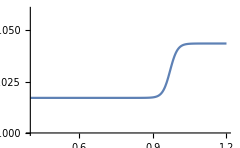

```mathematica
Plot[0.0171+CdW,{v,0.4,1.2},PlotRange->{0,0.06}]
```

```mathematica
CdW0=.;vM=.;dM=.;en=.;
```

-Graphics-

The lifts and drag are calculated from:

```mathematica
CDflat=1.;
CDfinflat=1.;
```

The lift coefficients. This model assumes all moving tailplane that is used on supersonic aircraft.

```mathematica
CLl1=CLift[Alpha1,CLalpha1e,ap1,an1,awp1,awn1]/2+CLde1 del1+CLde12 del12;
CLr1=CLift[Alpha1,CLalpha1e,ap1,an1,awp1,awn1]/2+CLde1 der1+CLde12 der12;
CLl2=CLift[Alpha2+del2,CLalpha2e,ap2,an2,awp2,awn2]/2;
CLr2=CLift[Alpha2+der2,CLalpha2e,ap2,an2,awp2,awn2]/2;
Cdil1=CDragInd[Alpha1,AR1,e1e,CLalpha1e,ap1,an1,awp1,awn1]/2+Cdide1 (del1-de10)^2+Cdide12  (del12-de120)^2-Cdide112 (del1-de10) (del12-de120);
Cdir1=CDragInd[Alpha1,AR1,e1e,CLalpha1e,ap1,an1,awp1,awn1]/2+Cdide1 (der1-de10)^2+Cdide12  (der12-de120)^2-Cdide112 (der1-de10) (der12-de120);
Cdil2=CDragInd[Alpha2+del2,AR2,e2e,CLalpha2e,ap2,an2,awp2,awn2]/2;
Cdir2=CDragInd[Alpha2+der2,AR2,e2e,CLalpha2e,ap2,an2,awp2,awn2]/2;
CLfin = CLift[-β - CLdefin defin/CLalphafin, CLalphafin, afin, afin, awfin, awfin];

Cmr1=CMoment[Alpha1,Cm01,Cmfs1,ap1,an1,awp1,awn1]/2-Cmde1 der1-Cmde12 der12-CLr1 smc/4 transM[v,vM,dM];
Cml1=CMoment[Alpha1,Cm01,Cmfs1,ap1,an1,awp1,awn1]/2-Cmde1 del1-Cmde12 del12-CLl1 smc/4 transM[v,vM,dM];
```

```mathematica
CL1expr = (CLl1 + CLr1);
CL2expr = (CLl2 + CLr2);
Cd1expr = (Cdl1 + Cdr1);
Cd2expr = (Cdl2 + Cdr2);
CLtotexpr=(CLl1 + CLr1)+(CLl2 + CLr2)S2/S1+CLbh Sbh/S1 ;
CDtotexpr=(Cdl1 + Cdr1)+CdW+(Cdl2 + Cdr2)S2/S1+Cd0b Sbh/S1+ Cd0fin Sfin/S1;

CLbh = Sin[α] CLalphabh;
CLbv = Sin[-β] CLalphabv;

Alpha1 = α dah1- ia1;
Alpha2 = α dah2 - ia2;
```

### Weight and balance

```mathematica
massexpr=Me+Mfuel+Mcargo;
```

```mathematica
xbcgexpr = 1/mass(Me xbcge + Mfuel xfuel+Mcargo xcargo);
```

### LocalExpressions

The geometric data is made dimmensionless using wingspan or mean aerodynamic cord mac (here derived from the standard mean cord and a dimensionless factor mac0) as reference. In this way the whole aircraft is rescaled if aspect ratio or wing reference area is changed.

```mathematica
localExpressions = {
{b1,√(S1 AR1),"m","Wing span 1"},
{b2,√(S2 AR2),"m","Wing span 2"},
{smc,√(S1 /AR1),"m","Standard aerodynamic chord"},
{mac,mac0 smc,"m","Mean aerodynamic chord"},
{hthrust,hthrust0 b1,double,"","engine vert. pos"},
{Ix,Ix0 Me S1 AR1,double," ","Inertia moment Ix/(Me S1 AR1)"},
{Ixz,Ixz0 Me S1,double," ","Inertia moment"},
{Iy,Iy0 Me S1/AR1,double," ","Inertia moment Iy/(Me S1/AR1)"},
{Iz,Iz0 Me S1 /AR1,double," ","Inertia moment Iy/(Me S1/AR1)"},
{lc1,lc10 mac,double,"","norm. ctrl surf. 1 ac fr hinge lc1/sqrt(AR1 S1)"},
{lc2,lc20 mac,double,"","norm. ctrl surf. 2 ac fr hinge lc1/sqrt(AR1 S1)"},
{lc12,lc120 mac,double,"","norm. flap 1 ac fr hinge"},
{lcfin,lcfin0 mac,double,"","ctrl s. fin ac fr hinge"},
{rc1,rc10  b1,double,"m","norm. ctrl surface 1 mom. arm"},
{rc12,rc120  b1,double,"m","norm. ctrl surface 12 mom. arm"},
{rc2,rc20  b1,double,"m","norm. ctrl surface 1 mom. arm"},
{rcfin,rcfin0 mac,double,"m","norm. ctrl surf. fin mom. arm"},
{S2,S20 S1,double,"","norm. wing area 2"},
{Sbh,Sbh0 S1,double,"","norm. hor. proj. area"},
{Sbv,Sbv0 S1,double,"","norm.body vert. proj. area"},
{Sfin,Sfin0 S1,double,"","norm. fin area"},
{xbach,xbach0 mac,double," ","body ac. hor."},
{xbacv,xbacv0 mac,double," ","body ac vert."},
{xbcge,xbcge0 mac,double," ","body cg"},
{xcargo,xcargo0 mac,double," ","cargo pos."},
{xfuel,xfuel0 mac,double," ",""},
{xw1,xw10 mac,double," ","wing1  position"},
{xw2,xw20 mac,double," ","wing 2 position"},
{xwfin,xwfin0 mac,double,"",""},
{xeng,xeng0  mac,double,"m","engines x-pos"},
{yeng,yeng0  b1,double,"m","engines off. from center"},
{betaM,((1-(v/vM)^2)^2+(epsM v/vM)^2)^(1/4),double,"Mach effect on lift"},
{CLalpha1e,CLalpha1/betaM,double,"Effective lift sloop"},
{CLalpha2e,CLalpha2/betaM,double,"Effective lift sloop"},
{e1e,e1 -e1(1-1/AR1) transM[v,vM,dM],double,"Effective oswald efficieny 1"},
{e2e,e2 -e2(1-1/AR2) transM[v,vM,dM],double,"Effective oswald efficieny 2"},
{v,Subscript[v, expr],double,"Abs. value of speed"},
{α,Subscript[α, expr],double,"Angle of attack"},
{q,Subscript[q, expr],double,"Dynamic pressure"},
{β,Subscript[β, expr],double,"Slip angle"},
{mass ,massexpr,double,"total AC-weight"},
{xbcg, xbcgexpr,double,"AC-cg"},
{Dragl1,Dragl1expr,double,"Drag from wing 1"},
{Dragr1,Dragr1expr,double,"Drag from wing 1"},
{Liftl1,Liftl1expr,double,"Lift from wing 1"},
{Liftr1,Liftr1expr,double,"Lift from wing 1"},
{Dragl2,Dragl2expr,double,"Drag from wing 2"},
{Dragr2,Dragr2expr,double,"Drag from wing 2"},
{Liftl2,Liftl2expr,double,"Lift from wing 2"},
{Liftr2,Liftr2expr,double,"Lift from wing 2"},
{Liftb,Liftbexpr,double,"Lift from body"},
{Dragb,Dragbexpr,double,"Drag from body"},
{Cfin,Cfinexpr,double,"Force from vertical tail"},
{Cl2,Cl2expr,double,"Side force from left canard"},
{Cr2,Cr2expr,double,"Side force from right canard"},
{Dragfin,Dragfinexpr,double,"Drag from body"},
{Subscript[M, θ̇] ,Subscript[Subscript[M, θ̇], expr],double,"Damping term in pitch"},
{Subscript[M, ψ̇],Subscript[Subscript[M, ψ̇], expr],double,"Damping term in yaw"},
{Fx,aircraft`F[[1]][[1]],double,"Force in x"},
{Fy,aircraft`F[[2]][[1]],double,"Force in y"},
{Fz,aircraft`F[[3]][[1]],double,"Force in z"},
{Lb,aircraft`T[[1]][[1]],double,"moment on x-axis"},
{Mb,aircraft`T[[2]][[1]],double,"moment on y-axis"},
{Nb,aircraft`T[[3]][[1]],double,"moment on z-axis"}};
```

```mathematica
expressions=Flatten[{expression,expressionVE,{
{AlphaAttack,α},
{BetaSlip,β},
{altitude,-zcg},
{ϕ,Subscript[ϕ, expr]},
{θ,Subscript[θ, expr]},
{ψ,Subscript[ψ, expr]},
{gfx,Fx/mass},
{gfy,Fy/mass},
{gfz,Fz/mass},
{Faz,aircraft`aero`Fw[[3]][[1]]},
{Fax,aircraft`aero`Fw[[1]][[1]]},
{CL1,CLtotexpr},
{Cd1,CDtotexpr},
{Zxfin,kafin mTimestep},
{Zxal1,kal1 mTimestep},
{Zxar1,kar1 mTimestep},
{Zxal12,kal12 mTimestep},
{Zxar12,kar12 mTimestep},
{Zxal2,kal2 mTimestep},
{Zxar2,kar2 mTimestep}
}},1];
```

```mathematica
Compgen[file]
```

Part::partd: Part specification delayedPart ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification xcg ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification 0. ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Set::partw: Part 101 of {afin, an1, an2, ap1, ap2, AR1, AR2, ARfin, Cd01, Cd02, Cd0b, Cd0fin, CdW0, CLalpha1, CLalpha2, CLalphabh, CLalphabv, CLalphafin, CLde1, CLde12, Cdide1, Cdide12, Cdide112, de10, « 3 », Cmfs1, Cmde1, Cmde12, CLdefin, Cydeelev, dah1, dah2, en, e1, e2, efin, epsM, awfin, awn1, awn2, awp1, awp2, gamma1, gamma2, hthrust0, ia1, ia2, Ix0, « 50 »} does not exist.

Set::partw: Part 102 of {afin, an1, an2, ap1, ap2, AR1, AR2, ARfin, Cd01, Cd02, Cd0b, Cd0fin, CdW0, CLalpha1, CLalpha2, CLalphabh, CLalphabv, CLalphafin, CLde1, CLde12, Cdide1, Cdide12, Cdide112, de10, « 3 », Cmfs1, Cmde1, Cmde12, CLdefin, Cydeelev, dah1, dah2, en, e1, e2, efin, epsM, awfin, awn1, awn2, awp1, awp2, gamma1, gamma2, hthrust0, ia1, ia2, Ix0, « 50 »} does not exist.

Set::partw: Part 103 of {afin, an1, an2, ap1, ap2, AR1, AR2, ARfin, Cd01, Cd02, Cd0b, Cd0fin, CdW0, CLalpha1, CLalpha2, CLalphabh, CLalphabv, CLalphafin, CLde1, CLde12, Cdide1, Cdide12, Cdide112, de10, « 3 », Cmfs1, Cmde1, Cmde12, CLdefin, Cydeelev, dah1, dah2, en, e1, e2, efin, epsM, awfin, awn1, awn2, awp1, awp2, gamma1, gamma2, hthrust0, ia1, ia2, Ix0, « 50 »} does not exist.

General::stop: Further output of Set :: partw will be suppressed during this calculation.

Part::partw: Part 101 of {afin, an1, an2, ap1, ap2, AR1, AR2, ARfin, Cd01, Cd02, Cd0b, Cd0fin, CdW0, CLalpha1, CLalpha2, CLalphabh, CLalphabv, CLalphafin, CLde1, CLde12, Cdide1, Cdide12, Cdide112, de10, « 3 », Cmfs1, Cmde1, Cmde12, CLdefin, Cydeelev, dah1, dah2, en, e1, e2, efin, epsM, awfin, awn1, awn2, awp1, awp2, gamma1, gamma2, hthrust0, ia1, ia2, Ix0, « 50 »} does not exist.

Part::partw: Part 102 of {afin, an1, an2, ap1, ap2, AR1, AR2, ARfin, Cd01, Cd02, Cd0b, Cd0fin, CdW0, CLalpha1, CLalpha2, CLalphabh, CLalphabv, CLalphafin, CLde1, CLde12, Cdide1, Cdide12, Cdide112, de10, « 3 », Cmfs1, Cmde1, Cmde12, CLdefin, Cydeelev, dah1, dah2, en, e1, e2, efin, epsM, awfin, awn1, awn2, awp1, awp2, gamma1, gamma2, hthrust0, ia1, ia2, Ix0, « 50 »} does not exist.

Part::partw: Part 103 of {afin, an1, an2, ap1, ap2, AR1, AR2, ARfin, Cd01, Cd02, Cd0b, Cd0fin, CdW0, CLalpha1, CLalpha2, CLalphabh, CLalphabv, CLalphafin, CLde1, CLde12, Cdide1, Cdide12, Cdide112, de10, « 3 », Cmfs1, Cmde1, Cmde12, CLdefin, Cydeelev, dah1, dah2, en, e1, e2, efin, epsM, awfin, awn1, awn2, awp1, awp2, gamma1, gamma2, hthrust0, ia1, ia2, Ix0, « 50 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

XMLElement::cntsList: XMLElement["modelobject", {"typename" → "AeroAircraft6DOFSS", "" … "" → « 20 »}, {XMLElement["icon", {"isopath" → "AeroAircraft6DOFSS.svg", "iconrotation" → "ON", "userpath" → "AeroAircraft6DOFSS.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → "0", "y" → 0.125, "a" → "0", "name" → "Pal1"}, {}], « 49 », « 2 »}]}] in XMLElement["hopsanobjectappearance", {"version" → "0.1"}, XMLElement["modelobject", {"typename" → "AeroAircraft6DOFSS", "displayname" → "AeroAircraft6DOFSS"}, {XMLElement["icon", {"isopath" → "AeroAircraft6DOFSS.svg", "iconrotation" → "ON", "userpath" → "AeroAircraft6DOFSS.svg"}, {}], « 1 »}]] is not a list of contents. The third item in an XMLElement must be a list of contents, even if it is an empty list.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.125 in "y" → 0.125 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.25 in "y" → 0.25 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

General::stop: Further output of Export :: autofix will be suppressed during this calculation.

XMLElement::attrhs: 0.375 in "y" → 0.375 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

General::stop: Further output of XMLElement :: attrhs will be suppressed during this calculation.